```mathematica
a=5;
b=5;
f0[x_,y_]:=x+ y;
f[x_,y_]:=f0[ x,y]/(Sinh [(π b)/a]) Sin[(π x)/a]  +Sinh[π y/a]
```

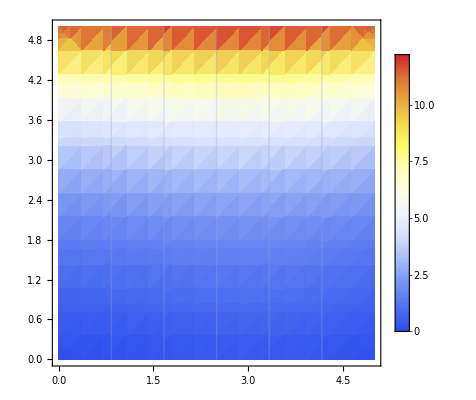

```mathematica
DensityPlot[f[x,y],{x,0,5},{y,0,5},Mesh->5, ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

```mathematica
Table[DiscretePlot3D[Mod[m,n],{m,15},{n,15},Filling->None,Evaluate[opt]],{opt,{Joined->False,Joined->True,ExtentSize->Full}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
test =Plot3D[f[x,y],{x,0,4},{y,0,4},PlotStyle->Pink, Mesh -> 4] ;
test2 =DiscretePlot3D[f[x,y],{x,0,4,1},{y,0,4,1},PlotStyle->Blue,Filling->None,ExtentSize->Full];  (*5^1 -> Step (5^-0) *) 
Show[test,test2]
```

-Graphics3D-

```mathematica
cHeat =Plot3D[f[x,y],{x,0,4},{y,0,4},PlotStyle->Pink, Mesh -> None]
pd5 =DiscretePlot3D[f[x,y],{x,0,4,1},{y,0,4,1},PlotStyle->Blue,Filling->None,ExtentSize->Full];  (*5^1 -> Step (5^-0) *) 
pd25 =DiscretePlot3D[f[x,y],{x,0,4,0.2},{y,0,4,0.2},PlotStyle->Green,Filling->None,ExtentSize->Full] (*5^2 -> Step (5^-1)*)
pd125 =DiscretePlot3D[f[x,y],{x,0,4,0.04},{y,0,4,0.04},PlotStyle->Yellow,Filling->None,ExtentSize->Full] (*5^2 -> Step (5^-2)*)
pd625 =DiscretePlot3D[f[x,y],{x,0,4,0.008},{y,0,4,0.008},PlotStyle->Orange,Filling->None,ExtentSize->Full](*5^4* -> Step (5^-3)*)
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
Show[cHeat,pd5, pd25,pd125,pd625]
```

-Graphics3D-

```mathematica
Show[pd5, pd25,pd125]
```

-Graphics3D-

```mathematica
DiscretePlot3D[PDF[MultivariatePoissonDistribution[3,{1,1}],{t,u}],{t,0,10},{u,0,10}]
```

-Graphics3D-

```mathematica
plot=Plot3D[f[x,y],{x,0,5},{y,0,5},PlotStyle->Directive[Opacity[0.4],Yellow],RegionFunction->(#<0||#2>0&)]
```

-Graphics3D-

```mathematica
plotDiscrete=DiscretePlot3D[f[x,y],{x,0,5},{y,0,5},PlotStyle->Directive[Opacity[1],Yellow],RegionFunction->(#<0||#2>0&)]
```

-Graphics3D-



```mathematica
Plot[Sin[x],{x,0,2 Pi}]
```

```mathematica
plot=Plot[Sin[x],{x,0,2 Pi},PlotStyle->Thick];
```

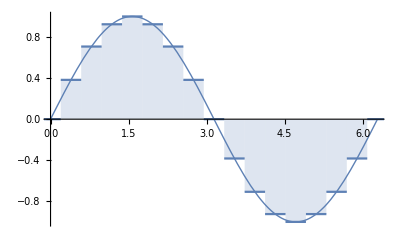
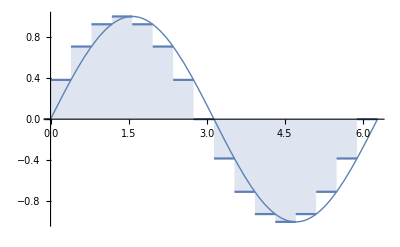
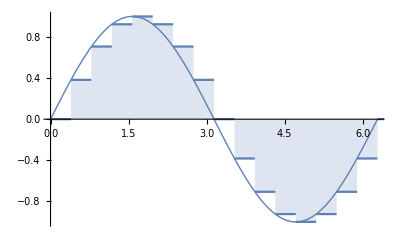

```mathematica
Table[Show[plot,DiscretePlot[Sin[x],{x,0,2 Pi,Pi/8},ExtentSize->s,PlotLabel->s]],{s,{Full,Left,Right}}]
```

```mathematica
plot=Plot3D[PDF[BinormalDistribution[0.5],{x,y}],{x,-2,2},{y,-2,2},PlotStyle->Directive[Opacity[0.4],Yellow],RegionFunction->(#<0||#2>0&)]
```

-Graphics3D-

```mathematica
riemann=DiscretePlot3D[PDF[BinormalDistribution[0.5],{x,y}],{x,-2,2,0.5},{y,-2,2,0.5},ExtentSize->Full,RegionFunction->(#<0||#2>0&)]
```

-Graphics3D-

```mathematica
Show[plot,riemann]
```

-Graphics3D-

-Graphics3D-